```mathematica
data=StringSplit[Import["/home/johannes/Documents/USA/courses/algo/finalproject/src_develop/cluster.out"],"\n"]
```

{Group 0,0.037945	0.317386	0.228511	,0.036863	0.936899	0.027154	,0.278705	0.284767	0.321606	,0.267904	0.285712	0.210186	,0.273741	0.253256	0.177423	,0.364215	0.847995	0.282942	,0.174239	0.976696	0.636979	,Group 1,0.923687	0.278837	0.692197	,0.394974	0.394754	0.810024	,0.128700	0.354037	0.692535	,0.657176	0.182671	0.536187	,0.349373	0.557864	0.810168	,0.976606	0.179280	0.634932	,0.186792	0.453022	0.888188	,0.866774	0.643979	0.895963	,Group 2,0.375193	0.273982	0.049963	,0.667284	0.258984	0.257350	,0.399336	0.595809	0.127555	,0.627847	0.632672	0.064453	,0.655000	0.911377	0.349220	}

```mathematica
ListPointPlot3D[{ToExpression[StringSplit[data[[2;;8]]]],ToExpression[StringSplit[data[[10;;17]]]],ToExpression[StringSplit[data[[19;;-1]]]]},PlotRange->{{0,1},{0,1},{0,1}},AspectRatio->1,PlotStyle->PointSize[Large]]
```

-Graphics3D-

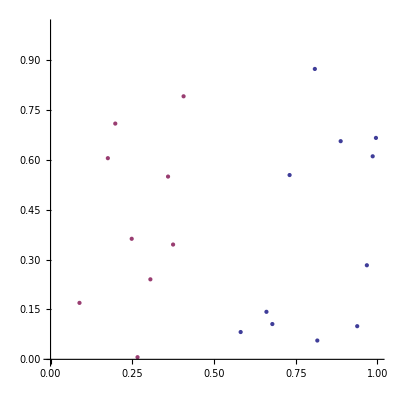

```mathematica
data[[16;;-1]]
```

{0.186792	0.453022	0.888188	,0.866774	0.643979	0.895963	,Group 2,0.375193	0.273982	0.049963	,0.667284	0.258984	0.257350	,0.399336	0.595809	0.127555	,0.627847	0.632672	0.064453	,0.655000	0.911377	0.349220	}

```mathematica
ListPointPlot3D[ToExpression[StringSplit[data[[2;;8]]]]]
```

-Graphics3D-

```mathematica
data[[10;;17]]
data[[19;;-1]]
```

{0.923687	0.278837	0.692197	,0.394974	0.394754	0.810024	,0.128700	0.354037	0.692535	,0.657176	0.182671	0.536187	,0.349373	0.557864	0.810168	,0.976606	0.179280	0.634932	,0.186792	0.453022	0.888188	,0.866774	0.643979	0.895963	}

{0.375193	0.273982	0.049963	,0.667284	0.258984	0.257350	,0.399336	0.595809	0.127555	,0.627847	0.632672	0.064453	,0.655000	0.911377	0.349220	}